```mathematica
S = 5.67*10^-8;
ALPHA = 9.7*10^-5;

(* EMISS = 0.75;  Anodized Aluminum Sphere *)
EMISS = 0.1;  (* Polished Aluminum Sphere *)


k=231;
DENS = 2702;
Cp=1033;
Dia=0.05;
R=0.025;
Tenv=300;
Tsur=300;
h=10;
dt=1;

Array [T1,100,0];
Ti=800;
Tfinal=400;
TIME[0]=0;

CONST =(EMISS)*S/(DENS*Cp*R/3);
```

```mathematica
i=4
TIME[i]= 1/CONST*NIntegrate[(1/(Tsur^4-T^4)),{T,Ti,Ti-(100*i)}]
TEMP=Ti-100*i
```

4

22334.1

400

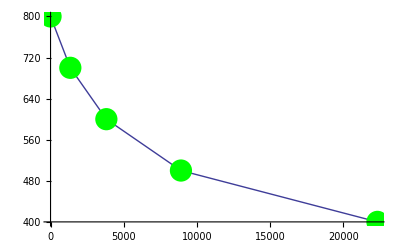

```mathematica
PlotPA=ListLinePlot[{{0,800}, {1351.9,700},{3813.6,600},{8908.6,500},{22334,400}},Mesh-> All,MeshStyle->{PointSize[0.04],Green}]
```

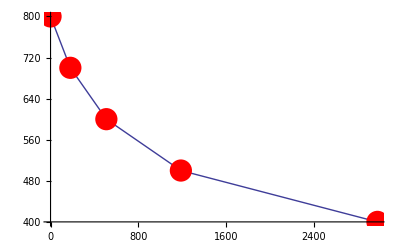

```mathematica
PlotAA=ListLinePlot[{{0,800}, {180.51,700},{508.48,600},{1187.2,500},{2977.9,400}},Mesh-> All,MeshStyle->{PointSize[0.04],Red}]
```

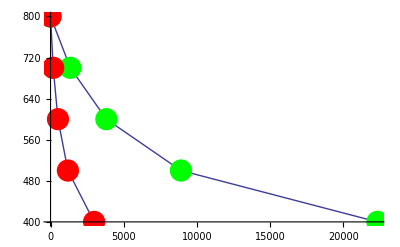

```mathematica
Show [PlotPA,PlotAA]
```

```mathematica
(* Now with Convection and Radiation *)
```

```mathematica
i=4
TIME[i]= 1/CONST2*NIntegrate[(1/(h*(Tenv-T)+EMISS*S*(Tsur^4-T^4))),{T,Ti,Ti-(100*i)}]
TEMP=Ti-100*i
```

4

3131.13

400

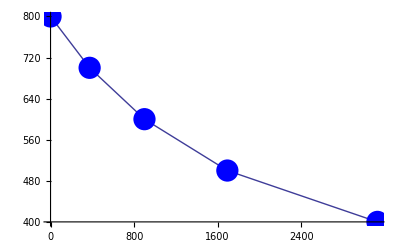

```mathematica
PlotRC=ListLinePlot[{{0,800}, {374.37,700},{899.6,600},{1693.4,500},{3131,400}},Mesh-> All,MeshStyle->{PointSize[0.04],Blue}]
```

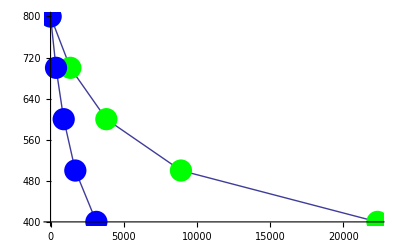

```mathematica
Show[PlotPA,PlotRC]
```

```mathematica
(*  Should be able to do this with a loop.

Do [T1[i]=Ti-100*i,{ i, 0,5}];
Do [Print [T1[i]], { i, 0,4}] 
800
700
600
500
400
Do [Print

NIntegrate[(1/(Tsur^4-T^4)),{T,Ti,T1[i]}]

,{i,0,4}] *)
```